```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\Critical-region\QCD\v1\delta\source

```mathematica
fpi=Flatten[Table[Import["./Tem"<>ToString[i]<>"/BUFFER/FPI.DAT"],{i,1,40}]];
Zphi=Flatten[Table[Import["./Tem"<>ToString[i]<>"/BUFFER/ZPHI.DAT"],{i,1,40}]];
fpi0=fpi(*/√Zphi*);
h=Flatten[Table[Import["./Tem"<>ToString[i]<>"/BUFFER/H.DAT"],{i,1,40}]];
(*h=h*√Zphi;*)
data=Transpose[{h,fpi}];
```

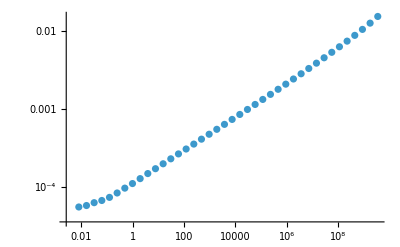

```mathematica
ListPlot[data,ScalingFunctions->{"Log","Log"}]
```

```mathematica
datalog=Transpose[{Log[h],Log[fpi0]}];
```

```mathematica
slop=Table[FindFit[datalog[[i;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,1,39}];
```

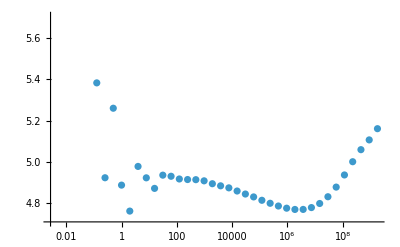

```mathematica
ListPlot[Transpose[{h[[1;;39]],1/slop}],ScalingFunctions->{"Log"}]
```